## Robot swarm with friction. Initial position is red rectangle.

```mathematica
Manipulate[(*controls: A, w, h, L*)
Module[{eps = 1/20,rside,rtop,rbot},
If[w<A,w=A];
Graphics[{
(*Text[xyCorr[L,w,A,h],{0,.6}],*)
{Pink,Rectangle[{-eps,-eps},{1+eps,1+eps}],White,Rectangle[{0,0},{1,1}]},
(*draw friction zone*)
{Opacity[0.5],ChartElementData["GradientRectangle","ColorScheme"->"PigeonTones","GradientOrigin"->Bottom][{{0,1},{0,h}}],
ChartElementData["GradientRectangle","ColorScheme"->"PigeonTones","GradientOrigin"->Top][{{0,1},{1-h,1}}]},
(*draw Robots*)
rtop   = Min[A/w,If[L>1-w, 1-   h/L (1-w), 1-h]];
rside = Min[L+w,1];
rbot   = Min[A/w,If[L>1-w,    h/L (1-w), h]];
(*bottom parallelogon*)
{Blue,Polygon[{{0,0},{w,0},{w+L/h rbot,rbot},{L/h rbot,rbot}}]},
(*middle rectangle*)
If[rtop>rbot,{Blue,Polygon[{{rside,rbot},{rside,rtop},{rside-w,rtop},{rside-w,rbot}}]}],
(*top parallelogon*)
If[A/w>rtop,{Blue,Polygon[{{rside, rtop},{rside-L/h (A/w-rtop),A/w },{rside-w-L/h (A/w-rtop),A/w},{rside-w,rtop}}]}],
(*initial robot config*)
{EdgeForm[{Red}],FaceForm[],Rectangle[{0,0},{w,A/w}]},
(*initial robot config*)
{Dashed,Gray,Line[{{0,h},{1,h}}],Line[{{0,1-h},{1,1-h}}]},

(*centroids of individual parts*)
{Purple,PointSize[Large],Point[{(w+L/h rbot)/2,rbot/2}]},
{Purple,PointSize[Large],Point[{ rside-w/2,(rbot+rtop)/2}]},
{Purple,PointSize[Large],Point[{ (rside-L/h (A/w-rtop)-w+rside)/2,(A/w+rtop)/2}]},

}]],
{{A,1/4},0.001,1},{w,0.001,1},{{h,1/8},0.0001,1/2 (*only stretch half the workspace*)},{L,0,2 (*we could make this bigger*)}
]
```

## Correlation as a function of Area of the robot swarm. assume robot swarm of total area A is initialized in a rectangle w wide by A/wtall in the lower left corner of a square workspace with sides of lenght 1. If the swarm is pushed to the right a distance L∈[0,1-w], and the boundary layer height is h, what is the maximum correlation?

```mathematica
Corxy[β_,A_]:=Which[A≤1/2,Piecewise[{{-(Tan[β] √(12 A^2-Tan[β]^2))/(√(48 A^4+24 A^2 Tan[β]^2-Tan[β]^4)), (0≤ β≤ ArcTan[2 A]) || (2 π - ArcTan[2 A] < β ≤  2π)}, {-1/2, ArcTan[2A]<β≤ π/2-ArcTan[2A]}, {-(Cot[β] √(12 A^2-Cot[β]^2))/(√(48 A^4+24 A^2 Cot[β]^2-Cot[β]^4)), π/2-ArcTan[2A]<β≤π/2+ArcTan[2A]}, {1/2, π/2+ArcTan[2A]< β≤ π-ArcTan[2A]}, {-(Tan[β] √(12 A^2-Tan[β]^2))/(√(48 A^4+24 A^2 Tan[β]^2-Tan[β]^4)), π-ArcTan[2 A]<β≤π+ArcTan[2 A]}, {-1/2, π+ArcTan[2A]< β≤ (3π)/2-ArcTan[2A]}, {-(Cot[β] √(12 A^2-Cot[β]^2))/(√(48 A^4+24 A^2 Cot[β]^2-Cot[β]^4)), (3π)/2-ArcTan[2A]<β≤(3π)/2+ArcTan[2A]}, {1/2, (3π)/2+ArcTan[2A]< β≤ 2π-ArcTan[2A]}}],
1/2<A<1,
Piecewise[{{-(Tan[β] √(12 A^2-Tan[β]^2))/(√(48 A^4+24 A^2 Tan[β]^2-Tan[β]^4)), (0≤ β≤ ArcTan[1/2,(1-A)]) || (2 π - ArcTan[1/2,(1-A)] < β ≤  2π)}, {((-1+A) (17+2 (-5+A) A-6 √2 (√((1-A) Cot[β])+ √((1-A)  Tan[β]))))/(√(-4 (-1+A)^2 (2+A) Cot[β]+3 (-3+4A+(1-A)4 √2 √((1-A)  Cot[β]))) √(-4 (-1+A)^2 (2+A) Tan[β]+3 (-3+4A+(1-A)4 √2 √((1-A)  Tan[β])))), ArcTan[1/2,(1-A)]< β≤ π/2-ArcTan[1/2,1-A]}, {-(Cot[β] √(12 A^2-Cot[β]^2))/(√(48 A^4+24 A^2 Cot[β]^2-Cot[β]^4)), π/2-ArcTan[1/2,1-A]<β≤ π/2+ArcTan[1/2,1-A]}, {-((-1+A) (17+2 (-5+A) A-6 √2 √((A-1) Cot[β])-6 √2 √((A-1) Tan[β])))/(√(4 (-1+A)^2 (2+A) Cot[β]+3 (-3+4A +4 (1-A)√2 √((A-1) Cot[β]))) √(4 (-1+A)^2 (2+A) Tan[β]+3 (-3+4A+(1-A)4 √2 √((A-1)Tan[β])))), π/2+ArcTan[1/2,1-A]< β≤ π-ArcTan[1/2,1-A]}, {-(Tan[β] √(12 A^2-Tan[β]^2))/(√(48 A^4+24 A^2 Tan[β]^2-Tan[β]^4)), π-ArcTan[1/2,1- A]<β≤ π+ArcTan[1/2,1- A]}, {((-1+A) (17+2 (-5+A) A-6 √2 (√((1-A) Cot[β])+ √((1-A)  Tan[β]))))/(√(-4 (-1+A)^2 (2+A) Cot[β]+3 (-3+4A+(1-A)4 √2 √((1-A)  Cot[β]))) √(-4 (-1+A)^2 (2+A) Tan[β]+3 (-3+4A+(1-A)4 √2 √((1-A)  Tan[β])))), π+ArcTan[1/2,1-A]< β≤ (3π)/2-ArcTan[1/2,1-A]}, {-(Cot[β] √(12 A^2-Cot[β]^2))/(√(48 A^4+24 A^2 Cot[β]^2-Cot[β]^4)), (3π)/2-ArcTan[1/2,1-A]<β≤ (3π)/2+ArcTan[1/2,1-A]}, {-((-1+A) (17+2 (-5+A) A-6 √2 √((A-1) Cot[β])-6 √2 √((A-1) Tan[β])))/(√(4 (-1+A)^2 (2+A) Cot[β]+3 (-3+4A +4 (1-A)√2 √((A-1) Cot[β]))) √(4 (-1+A)^2 (2+A) Tan[β]+3 (-3+4A+(1-A)4 √2 √((A-1)Tan[β])))), (3π)/2+ArcTan[1/2,1-A]< β≤2 π - ArcTan[1/2,(1-A)]}}],
A==1,0]
```

```mathematica
Plot[Corxy[3π/4,A],{A,0,1},PlotLegends->Placed[{"Gravity","Friction"},{Bottom,Center}],AxesLabel->{"A","Corr"}]
```

-Graphics-

### Compute Values for a linear friction boundray layer Assuming A/w>h,

```mathematica
xave = Simplify[(*rectangular part*)(∫_h^(A/w) (∫_L^(L+w) xⅆx)ⅆy+∫_0^h (∫_(L/h y)^(w+L/h y) xⅆx)ⅆy)/A]
yave = Simplify[(*rectangular part*)(∫_h^(A/w) (∫_L^(L+w) yⅆx)ⅆy+∫_0^h (∫_(L/h y)^(w+L/h y) yⅆx)ⅆy)/A]
xvar= FullSimplify[Simplify[(*rectangular part*)(∫_h^(A/w) (∫_L^(L+w) x^2 ⅆx)ⅆy)/A]+Simplify[(*parallelogram part*)(∫_0^h (∫_(L/h y)^(w+L/h y) x^2 ⅆx)ⅆy)/A]]-xave^2
yvar = FullSimplify[Simplify[(*rectangular part*)(∫_h^(A/w) (∫_L^(L+w) y^2 ⅆx)ⅆy)/A]+Simplify[(*parallelogram part*)(∫_0^h (∫_(L/h y)^(w+L/h y) y^2 ⅆx)ⅆy)/A]]-yave^2
covxy = 
FullSimplify[Simplify[(*rectangular part*)(∫_h^(A/w) (∫_L^(L+w) x*yⅆx)ⅆy)/A]+Simplify[(*parallelogram part*)(∫_0^h (∫_(L/h y)^(w+L/h y) x*yⅆx)ⅆy)/A]]-xave*yave
corxy=FullSimplify[covxy/(Sqrt[xvar]*Sqrt[yvar])]
```

(h w (L+w))/(2 A)+((2 L+w) (A-h w))/(2 A)

A/(2 w)

-((h w (L+w))/(2 A)+((2 L+w) (A-h w))/(2 A))^2+(-h L w (4 L+3 w)+2 A (3 L^2+3 L w+w^2))/(6 A)

A^2/(12 w^2)

-(h^2 L w)/(6 A)+(A (2 L+w))/(4 w)-(A ((h w (L+w))/(2 A)+((2 L+w) (A-h w))/(2 A)))/(2 w)

(h L (3 A-2 h w))/(A √(A^2/w^2) √((w (4 A h L^2+A^2 w-3 h^2 L^2 w))/A^2))

### Compute Values for a linear friction boundray layer Assuming A/w<h,Error: sum everything, then divide by A

```mathematica
xave = Simplify[(*parallelogram part*)(∫_0^h (∫_(L/h y)^(w+L/h y) xⅆx)ⅆy)/A]
yave = Simplify[(*parallelogram part*)(∫_0^h (∫_(L/h y)^(w+L/h y) yⅆx)ⅆy)/A]
xvar=Simplify[(*parallelogram part*)(∫_0^h (∫_(L/h y)^(w+L/h y) x^2 ⅆx)ⅆy)/A]-xave^2
yvar =Simplify[(*parallelogram part*)(∫_0^h (∫_(L/h y)^(w+L/h y) y^2 ⅆx)ⅆy)/A]-yave^2
covxy = +Simplify[(*parallelogram part*)(∫_0^h (∫_(L/h y)^(w+L/h y) x*yⅆx)ⅆy)/A]-xave*yave
corxy=FullSimplify[covxy/(Sqrt[xvar]*Sqrt[yvar])]
```

(h w (L+w))/(2 A)

(h^2 w)/(2 A)

-(h^2 w^2 (L+w)^2)/(4 A^2)+(h w (2 L^2+3 L w+2 w^2))/(6 A)

(h^3 w)/(3 A)-(h^4 w^2)/(4 A^2)

-(h^3 w^2 (L+w))/(4 A^2)+(h^2 w (4 L+3 w))/(12 A)

(h^2 w (-3 h w (L+w)+A (4 L+3 w)))/(A^2 √((h^3 w (4 A-3 h w))/A^2) √((h w (-3 h w (L+w)^2+A (4 L^2+6 L w+4 w^2)))/A^2))

```mathematica
xyCorr [L_,w_,A_,h_]:=If[A/w>h, (h L (3 A-2 h w))/(A √(A^2/w^2) √((w (4 A h L^2+A^2 w-3 h^2 L^2 w))/A^2)),(h^2 w (-3 h w (L+w)+A (4 L+3 w)))/(A^2 √((h^3 w (4 A-3 h w))/A^2) √((h w (-3 h w (L+w)^2+A (4 L^2+6 L w+4 w^2)))/A^2))]
```

```mathematica
As = 1/4;
hs = 1/3;
Plot3D[xyCorr [L,w,As,1],{L,0,1},{w,As,1},AxesLabel->{"L","w"},RegionFunction->Function[{L,w,z},L<1-w&&w<As/hs]]
```

-Graphics3D-

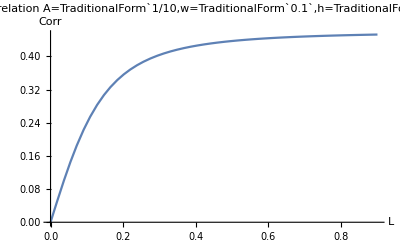

```mathematica
ws = .1;  (*must be > A*)
As = 1/10;
hs = 1/10;
(*xyCorr[L,w,A,h]*)
Plot[xyCorr [L,ws,As,hs],{L,0,1-ws},AxesLabel->{"L","Corr"},PlotLabel->StringForm["Correlation A=``,w=``,h=``",As,ws,hs],PlotRange->All]
```

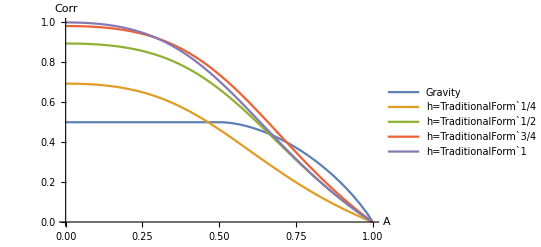

```mathematica
hs = {1/4,1/2,3/4,1};
(*xyCorr[L,w,A,h]*)
Plot[Evaluate[{Corxy[3π/4,A],Table[xyCorr [1-A,A,A,h],{h,hs}]}],{A,0,1},PlotLegends->Placed[Flatten[{"Gravity",Table[StringForm["h=``",h],{h,hs}]}],{Right,Center}],AxesLabel->{"A","Corr"}]
```

```mathematica
hs = {1/4,1/2,3/4,1};
(*xyCorr[L,w,A,h]*)
Plot[Evaluate[{Corxy[3π/4,A],Table[xyCorr [1-A,A,A,h],{h,hs}]}],{A,0,1},PlotLegends->Placed[Flatten[{"Gravity",Table[StringForm["h=``",h],{h,hs}]}],{Right,Center}],AxesLabel->{"A","Corr"}]
```

-Graphics-

```mathematica
yvar3 = FullSimplify[Simplify[(∫_0^(A/w) y^2 w ⅆy)/A]-(A/(2 w))^2]
```

A^2/(12 w^2)

```mathematica
yave3
```

A/(2 w)

```mathematica
rside-L/h (y-rtop)
```

```mathematica
xave1 = FullSimplify[(*lower parallelogram*)(∫_0^rbot (∫_(L/h y)^(L/h y+w) xⅆx)ⅆy)/(∫_0^rbot (∫_(L/h y)^(L/h y+w) ⅆx)ⅆy)]
xave2 = FullSimplify[(*rectangle*)(∫_rbot^rtop (∫_(rside-w)^rside xⅆx)ⅆy)/(∫_rbot^rtop (∫_(rside-w)^rside ⅆx)ⅆy)]
xave3 = FullSimplify[(*higher parallelogram*)(∫_rtop^(A/w) (∫_(rside-L/h (y-rtop)-w)^(rside-L/h (y-rtop)) xⅆx)ⅆy)/(∫_rtop^(A/w) (∫_(rside-L/h (y-rtop)-w)^(rside-L/h (y-rtop)) ⅆx)ⅆy)]
```

(L rbot+h w)/(2 h)

rside-w/2

1/2 (2 rside+(L (rtop-A/w))/h-w)

```mathematica
yave =A/(2 w);
xvar1= FullSimplify[Simplify[(∫_0^rbot (∫_(L/h y)^(w+L/h y) x^2 ⅆx)ⅆy)/A]-xave1^2];
xvar2= FullSimplify[Simplify[∫_0^rbot (∫_(L/h y)^(w+L/h y) x^2 ⅆx)ⅆy+∫_rbot^rtop (∫_(rside-w)^rside x^2 ⅆx)ⅆy]/A-(xave1+xave2)^2];
xvar3= FullSimplify[Simplify[∫_0^rbot (∫_(L/h y)^(w+L/h y) x^2 ⅆx)ⅆy+∫_rbot^rtop (∫_(rside-w)^rside x^2 ⅆx)ⅆy+∫_rtop^(A/w) (∫_(rside-L/h (y-rtop)-w)^(rside-L/h (y-rtop)) x^2 ⅆx)ⅆy]/A-(xave1+xave2+xave3)^2];
yvar =A^2/(12 w^2);
covxy1 = FullSimplify[Simplify[(*lower parallelogram*)(∫_0^rbot (∫_(L/h y)^(w+L/h y) x*yⅆx)ⅆy)/A]-xave1*yave];
covxy2 = FullSimplify[Simplify[∫_0^rbot (∫_(L/h y)^(w+L/h y) x*yⅆx)ⅆy+∫_rbot^rtop (∫_(rside-w)^rside x*yⅆx)ⅆy]/A-(xave1+xave2)*yave];
covxy3 = FullSimplify[Simplify[∫_0^rbot (∫_(L/h y)^(w+L/h y) x*yⅆx)ⅆy+∫_rbot^rtop (∫_(rside-w)^rside x*yⅆx)ⅆy+∫_rtop^(A/w) (∫_(rside-L/h (y-rtop)-w)^(rside-L/h (y-rtop)) x*yⅆx)ⅆy]/A-(xave1+xave2+xave3)*yave];
corxy1=FullSimplify[covxy1/(Sqrt[xvar1]*Sqrt[yvar])]
corxy2=FullSimplify[covxy2/(Sqrt[xvar2]*Sqrt[yvar])]
corxy3=FullSimplify[covxy3/(Sqrt[xvar3]*Sqrt[yvar])]
```

(A (-3 A^2 (L rbot+h w)+rbot^2 w^2 (4 L rbot+3 h w)))/(h (A^2/w^2)^(3/2) w^3 √((-3 A (L rbot+h w)^2+2 rbot w (2 L^2 rbot^2+3 h L rbot w+2 h^2 w^2))/(A h^2)))

(A (-3 A^2 (L rbot+2 h rside)+w^2 (4 L rbot^3-3 h (2 rbot^2 (rside-w)+rtop^2 (-2 rside+w)))))/(h (A^2/w^2)^(3/2) w^3 √((-3 A (L rbot+2 h rside)^2+2 w (2 L^2 rbot^3+3 h L rbot^2 w+2 h^2 (3 rside^2 (-rbot+rtop)+3 rside (rbot-rtop) w+rtop w^2)))/(A h^2)))

-((A (A^3 L+3 A^2 (2 h rside+L (rbot-rtop)) w+2 (L (-2 rbot^3+rtop^3)+3 h rbot^2 (rside-w)) w^3))/(h (A^2/w^2)^(3/2) w^4 √(1/(A h^2 w^2)(A^3 L^2+6 A^2 L (2 h rside+L (rbot-rtop)) w+A w^2 (-3 (2 h rside+L (rbot-rtop)) (6 h rside+L (rbot+3 rtop))+6 h (2 h rside+L (rbot-rtop)) w+h^2 w^2)+2 w^3 (2 L^2 (rbot^3-rtop^3)+6 h^2 rbot rside (-rside+w)+3 h L (rbot^2 w+rtop^2 (-2 rside+w)))))))

```mathematica
Clear[cor1,cor2,cor3];
cor1[A_,L_,h_,w_,rbot_]:=(A (-3 A^2 (L rbot+h w)+rbot^2 w^2 (4 L rbot+3 h w)))/(h (A^2/w^2)^(3/2) w^3 √((-3 A (L rbot+h w)^2+2 rbot w (2 L^2 rbot^2+3 h L rbot w+2 h^2 w^2))/(A h^2)))
cor2[A_,L_,h_,w_,rbot_,rside_,rtop_]:=(A (-3 A^2 (L rbot+2 h rside)+w^2 (4 L rbot^3-3 h (2 rbot^2 (rside-w)+rtop^2 (-2 rside+w)))))/(h (A^2/w^2)^(3/2) w^3 √((-3 A (L rbot+2 h rside)^2+2 w (2 L^2 rbot^3+3 h L rbot^2 w+2 h^2 (3 rside^2 (-rbot+rtop)+3 rside (rbot-rtop) w+rtop w^2)))/(A h^2)))
cor3[A_,L_,h_,w_,rbot_,rside_,rtop_]:=-((A (A^3 L+3 A^2 (2 h rside+L (rbot-rtop)) w+2 (L (-2 rbot^3+rtop^3)+3 h rbot^2 (rside-w)) w^3))/(h (A^2/w^2)^(3/2) w^4 √(1/(A h^2 w^2)(A^3 L^2+6 A^2 L (2 h rside+L (rbot-rtop)) w+A w^2 (-3 (2 h rside+L (rbot-rtop)) (6 h rside+L (rbot+3 rtop))+6 h (2 h rside+L (rbot-rtop)) w+h^2 w^2)+2 w^3 (2 L^2 (rbot^3-rtop^3)+6 h^2 rbot rside (-rside+w)+3 h L (rbot^2 w+rtop^2 (-2 rside+w)))))))
```

```mathematica
{xave1,yave}
{xave2,yave}
{xave3,yave}
```

{(rbot w (L rbot+h w))/(2 A h),A/(2 w)}

{(w (L rbot^2+h (-2 rbot rside+2 rside rtop+2 rbot w-rtop w)))/(2 A h),A/(2 w)}

{(-A^2 L+A w (2 h rside+2 L rtop-h w)+w^2 (L (rbot^2-rtop^2)+2 h rbot (-rside+w)))/(2 A h w),A/(2 w)}

TODO: show mean, show correlation, etc.

```mathematica
Manipulate[(*controls: A, w, h, L*)
Module[{eps = 1/20,rside,rtop,rbot},
If[w<A,w=A];
Graphics[{
(*Text[xyCorr[L,w,A,h],{0,.6}],*)
{Pink,Rectangle[{-eps,-eps},{1+eps,1+eps}],White,Rectangle[{0,0},{1,1}]},
(*draw friction zone*)
{Opacity[0.5],ChartElementData["GradientRectangle","ColorScheme"->"PigeonTones","GradientOrigin"->Bottom][{{0,1},{0,h}}],
ChartElementData["GradientRectangle","ColorScheme"->"PigeonTones","GradientOrigin"->Top][{{0,1},{1-h,1}}]},
(*draw Robots*)
rtop   = Min[A/w,If[L>1-w, 1-   h/L (1-w), 1-h]];
rside = Min[L+w,1];
rbot   = Min[A/w,If[L>1-w,    h/L (1-w), h]];
(*bottom parallelogon*)
{Blue,Polygon[{{0,0},{w,0},{w+L/h rbot,rbot},{L/h rbot,rbot}}]},
(*middle rectangle*)
If[rtop>rbot,{Blue,Polygon[{{rside,rbot},{rside,rtop},{rside-w,rtop},{rside-w,rbot}}]}],
(*top parallelogon*)
If[A/w>rtop,{Blue,Polygon[{{rside, rtop},{rside-L/h (A/w-rtop),A/w },{rside-w-L/h (A/w-rtop),A/w},{rside-w,rtop}}]}],
(*initial robot config*)
{EdgeForm[{Red}],FaceForm[],Rectangle[{0,0},{w,A/w}]},
(*initial robot config*)
{Dashed,Gray,Line[{{0,h},{1,h}}],Line[{{0,1-h},{1,1-h}}]},

(*centroids of individual parts*)
{Purple,PointSize[Large],Point[{(w+L/h rbot)/2,rbot/2}]},
{Purple,PointSize[Large],Point[{ rside-w/2,(rbot+rtop)/2}]},
{Purple,PointSize[Large],Point[{ (rside-L/h (A/w-rtop)-w+rside)/2,(A/w+rtop)/2}]},

(*draw the mean*) (*Point[If[A/w>rtop, {xave3,yave3}, If[rtop>rbot,{xave2,yave2},{xave1,yave1}]*)
{Red,PointSize[Large],Point[{(L rbot+h w)/(2 h),A/(2 w)}]},
{Green,PointSize[Medium],Point[{rside-w/2,A/(2 w)}]},
{Yellow,PointSize[Medium],Point[{1/2 (2 rside+(L (rtop-A/w))/h-w),A/(2 w)}]},
Text[StringForm["Corr=``",
If[A/w>rtop,cor3[A,L,h,w,rbot,rside,rtop] ,
 If[rtop>rbot,cor2[A,L,h,w,rbot,rside,rtop],cor1[A,L,h,w,rbot,rside,rtop]]
]],{1/2,1/2}]

}]],
{{A,1/4},0.001,1},{w,0.001,1},{{h,1/8},0.0001,1/2 (*only stretch half the workspace*)},{L,0,2 (*we could make this bigger*)}
]
```

TODO : powerpoint of moves in square: odd move to wall, even moves minimize delta errors, last move to goal pose.